```mathematica
ep=0.008;β=0.7;γ=0.8;maxtime=10;xmin=-40;xmax=40;
Print["Critical ρ: ",Sqrt[2(1-β^2/3)]]
ρ=2.3;
```

```mathematica
Manipulate[
eqn=FindRoot[(1-ρ1^2/2)v-v^3/3-(v+β)/γ==0,{v,-1}];
v0=v/.eqn;
f[v_]=(1-ρ1^2/2)v-v^3/3;
eqn1=FindRoot[(1-ρ1^2/2-v0^2)v-v0 v^2-v^3/3==0,{v,0.5}];
eqn2=FindRoot[(1-ρ1^2/2-v0^2)v-v0 v^2-v^3/3==0,{v,2}];
v1=v/.eqn1;
v2=v/.eqn2;
Show[Plot[{-f[v+v0]+v0/γ+β/γ},{v,-1,2.5},PlotRange->{-3,3}],Graphics[{Red,Dashed,Line[{{v1,-5},{v1,5}}]}],Graphics[{Red,Dashed,Line[{{v2,-5},{v2,5}}]}]]
,{{ρ1,Sqrt[2(1-β^2/3)]},0,2,Appearance->"Open"}]

δ=0.5
Manipulate[
eqn=FindRoot[(1-ρ1^2/2)v-v^3/3-(v+β)/γ==0,{v,-1}];
v0=v/.eqn;
f[v_]=(1-ρ1^2/2)v-v^3/3;
h[v_]=Which[0<v<2.5,Min[-f[v+v0]+v0/γ,f[-v+v0]-v0/γ]];
f2[v_]=Which[v<v0,f[δ (v)],v>v0,f[v]];

Show[Plot[{-f[v+v0]+v0/γ-(v)/γ,-f[v+v0]+v0/γ,h[v]},{v,-2,4},PlotRange->{-4,4}],Plot[-β/γ,{v,-2,4},PlotStyle->{Dashed,Gray,Thick}]]
,{{ρ1,Sqrt[2(1-β^2/3)]},0,2.5,Appearance->"Open"}]


(*Print["Derivative at v=0: ",-(1-ρ^2/2-v0^2)]
Print["Compare with 1/γ: ",1/γ]
eqn3=FindRoot[-(1-ρ^2/2-v0^2)v+v0 v^2+v^3/3-v/γ==0,{v,-1}];
```

-0.451507

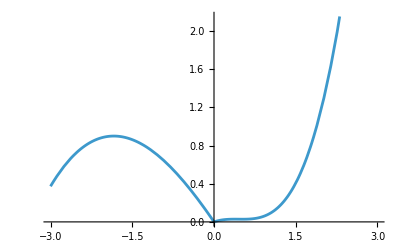

0.445936

{InterpolatingFunction[…],InterpolatingFunction[…]}

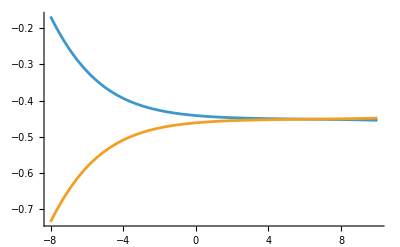

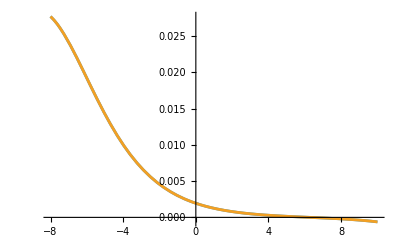

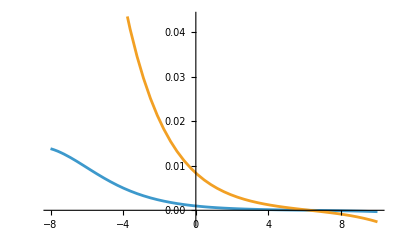

```mathematica
ρ=1.8;
f[v_]=(1-ρ^2/2)v-v^3/3 ;
eqn=FindRoot[-(1-ρ^2/2)v+v^3/3 + (v+β)/γ==0,{v,0}];
v0=v/.eqn
MM=0.01;
δ=0.5;
Plot[Which[v<0,-f[δ v+v0]+f[v0]-v/γ,True,-f[v+v0]+f[v0]-δ v/γ],{v,-3,3}]
Print[Sqrt[-(1-ρ^2/2)+v0^2-δ/γ]]
{V,U}=NDSolveValue[{v'[x]==u[x],u'[x]==-f[v[x]+v0]+(v0+β)/γ-δ v[x]/γ,v[0]==MM,u[0]==-MM Sqrt[-(1-ρ^2/2)+v0^2-δ/γ]},{v,u},{x,-8,10}]
(*ParametricPlot[{V[x],U[x]},{x,-5,3},PlotRange->{{-0.2,0.2},{-0.2,0.2}}]*)
Plot[{v0+V[x],v0-V[x]},{x,-8,10},PlotRange->All]
Plot[{V''[x],-f[V[x]+v0]+f[v0]-δ V[x]/γ},{x,-8,10}]
Plot[{δ V''[x],-f[-δ V[x]+v0]+f[v0]+V[x]/γ},{x,-8,10}]
(*
{V1,W1}=NDSolveValue[{D[u[t, x], t] == D[u[t, x], x, x] + u[t, x](1-ρ^2/2)-u[t,x]^3/3- w[t,x],  D[w[t, x], t] ==ep( u[t, x] - γ w[t, x]+β), 
u[0, x] ==v0+Which[Abs[x+9]<2,1,True,0], 
u[t, xmin] == v0, 
u[t, xmax] == v0, w[0, x] ==(v0+β)/γ}, {u, w}, {t, 0, maxtime}, {x, xmin, xmax}];
Animate[Show[Plot[V1[t,x],{x,xmin,xmax},PlotRange->{-1,2},PlotStyle->Red],Plot[{v0+V[x],v0-V[x]},{x,-8,0}]],{t,0,2,0.1},AnimationRunning->False]
*)
```

```mathematica
(*g1=Show[Plot[V1[0,x],{x,xmin,xmax},PlotRange->{-1,2},PlotStyle->Red,Frame->True],Plot[{v0+V[x],v0-V[x]},{x,-8,0}],ImageSize->Medium];
g2=Show[Plot[V1[0.3,x],{x,xmin,xmax},PlotRange->{-1,2},PlotStyle->Red,Frame->True],Plot[{v0+V[x],v0-V[x]},{x,-8,0}],ImageSize->Medium];
g3=Show[Plot[V1[0.6,x],{x,xmin,xmax},PlotRange->{-1,2},PlotStyle->Red,Frame->True],Plot[{v0+V[x],v0-V[x]},{x,-8,0}],ImageSize->Medium];
Grid[{{g1,g2,g3}}]*)
```